```mathematica
ClearAll["Global`*"];
```

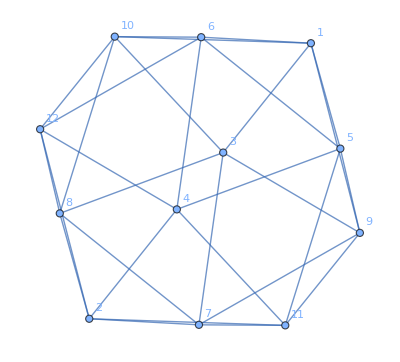

```mathematica
(* =========================1. Graph=========================*)bonds1Based={{1,3},{1,5},{1,6},{1,9},{1,10},{2,4},{2,7},{2,8},{2,11},{2,12},{3,7},{3,8},{3,9},{3,10},{4,5},{4,6},{4,11},{4,12},{5,6},{5,9},{5,11},{6,10},{6,12},{7,8},{7,9},{7,11},{8,10},{8,12},{9,11},{10,12}};

g=Graph[Range[12],UndirectedEdge@@@bonds1Based,VertexLabels->"Name"];

g(*optional to display*)
```

```mathematica
(* ====================2. Automorphism group====================*)
A=GraphAutomorphismGroup[g];
GroupOrder[A]        (*should be 120*)
```

120

```mathematica
(* ====================3. All group elements as lists====================*)(*Get all group elements as PermutationGroupElement/Cycles objects*)
elems=GroupElements[A];

(*Convert each element to a permutation list on {1,...,12} so that perm[[i]] is the image of i*)
elemsList=PermutationList[#,12]&/@elems;

Length[elemsList]    (*should be 120*)
```

120

```mathematica
(* ====================4. Basic permutation utilities====================*)

(*Composition:p∘q (apply q first,then p)*)
permCompose[p_List,q_List]:=p[[q]];

(*Inverse permutation*)
permInverse[p_List]:=Module[{inv=ConstantArray[0,Length[p]]},Do[inv[[p[[i]]]]=i,{i,Length[p]}];
inv];

(*Order of a permutation (small,so brute force is fine)*)
permOrder[p_List]:=Module[{e=Range[Length[p]],x=p,k=1},While[x=!=e,x=permCompose[p,x];
k++;];
k];
```

```mathematica
(* ====================5. Conjugacy classes (manual)====================*)conjugacyClasses=Module[{unseen=elemsList,classes={},rep,cls},While[unseen=!={},rep=First[unseen];
cls=Union[Table[Module[{h=elemsList[[k]],hinv},hinv=permInverse[h];
permCompose[h,permCompose[rep,hinv]]],{k,Length[elemsList]}]];
AppendTo[classes,cls];
unseen=Complement[unseen,cls];];
classes];

Length[conjugacyClasses]    (*should be 10*)
```

10

```mathematica
(* ====================6. Inspect sizes& orders====================*)classInfo=Table[<|"ClassIndex"->i,"Size"->Length[conjugacyClasses[[i]]],"OrderOfRepresentative"->permOrder[conjugacyClasses[[i,1]]],"Representative1Based"->conjugacyClasses[[i,1]]|>,{i,Length[conjugacyClasses]}];

classInfo

(*You should see sizes like {1,1,12,12,12,12,15,15,20,20} and orders 1,2,5,5,3,10,2,2,6,3 (up to reordering).*)
```

{<|ClassIndex→1,Size→1,OrderOfRepresentative→1,Representative1Based→{1,2,3,4,5,6,7,8,9,10,11,12}|>,<|ClassIndex→2,Size→15,OrderOfRepresentative→2,Representative1Based→{1,2,3,4,6,5,8,7,10,9,12,11}|>,<|ClassIndex→3,Size→12,OrderOfRepresentative→5,Representative1Based→{1,2,5,8,10,3,4,11,6,9,12,7}|>,<|ClassIndex→4,Size→12,OrderOfRepresentative→5,Representative1Based→{1,2,9,12,6,10,11,7,5,3,4,8}|>,<|ClassIndex→5,Size→15,OrderOfRepresentative→2,Representative1Based→{2,1,4,3,7,8,5,6,11,12,9,10}|>,<|ClassIndex→6,Size→1,OrderOfRepresentative→2,Representative1Based→{2,1,4,3,8,7,6,5,12,11,10,9}|>,<|ClassIndex→7,Size→12,OrderOfRepresentative→10,Representative1Based→{2,1,7,6,4,12,9,3,11,8,5,10}|>,<|ClassIndex→8,Size→12,OrderOfRepresentative→10,Representative1Based→{2,1,11,10,12,8,5,9,4,7,6,3}|>,<|ClassIndex→9,Size→20,OrderOfRepresentative→6,Representative1Based→{3,4,7,6,10,1,2,11,8,9,12,5}|>,<|ClassIndex→10,Size→20,OrderOfRepresentative→3,Representative1Based→{3,4,9,12,10,8,5,11,1,7,6,2}|>}

```mathematica
(* ====================7. Convert to 0-based for Python====================*)
conjugacyClasses0Based=(#-1)&/@conjugacyClasses;

(*One example:show size and a sample permutation (0-based) per class*)
Table[<|"ClassIndex"->i,"Size"->Length[conjugacyClasses0Based[[i]]],"ExamplePerm0Based"->conjugacyClasses0Based[[i,1]]|>,{i,Length[conjugacyClasses0Based]}];
```

```mathematica
(* ====================8. Optional export====================*)(*Flat list of all 120 permutations in 0-based form*)(*Flat list of all 120 permutations (0-based)*)
allPerms0Based=Flatten[conjugacyClasses0Based,1];
(*Format each permutation as a Python-style list string*)
stringPerms="["<>StringRiffle[ToString/@#,", "]<>"]"&/@allPerms0Based;

Directory[]
(*Export each permutation on its own line*)
Export["C:\\Users\\camipolv\\Desktop\\ih_permutations_0based.txt",stringPerms,"Lines"]
(*Grouped by classes (10 blocks),still 0-based*)
Export["C:\\Users\\camipolv\\Desktop\\ih_conjugacy_classes_0based.m",conjugacyClasses0Based,"Table"];
```

C:\Users\camipolv

C:\Users\camipolv\Desktop\ih_permutations_0based.txt